# Question 01

```mathematica
Exit[]
```

Clear

```mathematica
sol1=DSolve[y'[x]+Cos[x]*y[x]==0,y[x],x]
table1=Table[sol1[[1,1,2]]/.C[1]->i,{i,-5,5}];
```

{{y[x]→ⅇ^(-Sin[x]) C[1]}}

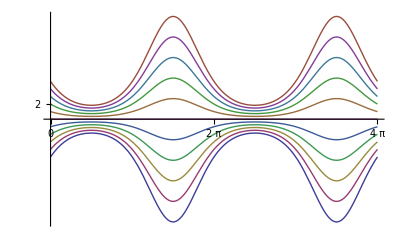

```mathematica
Plot[table1,{x,0,4*Pi},Ticks->{{0,2*Pi,4*Pi},{2}}]
```

# Question 02

```mathematica
a1=NDSolveValue[{x''[t]+(1/3*x'[t]^2-1)*x'[t]+x[t]==0,x[0]==.1,x'[0]==0},x[t],{t,0,15}];
a2=NDSolveValue[{x''[t]+(1/3*x'[t]^2-1)*x'[t]+x[t]==0,x[0]==1,x'[0]==0},x[t],{t,0,15}];a3=NDSolveValue[{x''[t]+(1/3*x'[t]^2-1)*x'[t]+x[t]==0,x[0]==1.9,x'[0]==0},x[t],{t,0,15}]
```

InterpolatingFunction[{{0.,15.}},<>][t]

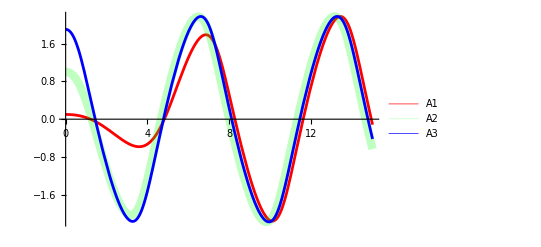

```mathematica
Plot[{a1,a2,a3},{t,0,15},PlotLegends->{"A1","A2","A3"},PlotStyle->{{RGBColor[1,0,0],Thickness[.005]},{RGBColor[0,1,0],Thickness[.015],Opacity[.25]},{RGBColor[0,0,1],Thickness[.005]}}]
```

# Question 03

```mathematica
m=1;k=.3;a=.04;
table3=Table[NDSolveValue[{m*x''[t]+k*x'[t]+a*x[t]^3==0,x[0]==0,x'[0]==i},x[t],{t,0,15}],{i,1,5}]
```

{InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t],InterpolatingFunction[{{0.,15.}},<>][t]}

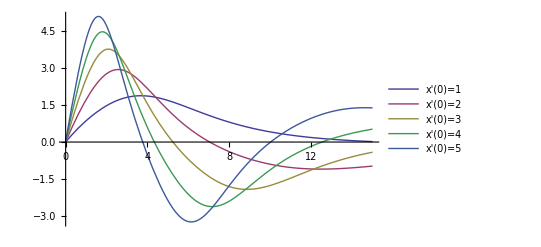

```mathematica
Plot[table3,{t,0,15},PlotLegends->{"x'(0)=1","x'(0)=2","x'(0)=3","x'(0)=4","x'(0)=5"}]
```

# Question 04

```mathematica
σ=10;β=8/3;ρ=28;
table4=NDSolveValue[{x'[t]==σ*(y[t]-x[t]),y'[t]==ρ*x[t]-y[t]-x[t]*z[t],z'[t]==x[t]*y[t]-z[t]*β,x[0]==10,y[0]==10,z[0]==10},{x[t],y[t],z[t]},{t,0,50}]
```

{InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t],InterpolatingFunction[{{0.,50.}},<>][t]}

```mathematica
ParametricPlot3D[table4,{t,0,50}]
```

-Graphics3D-

# Question 05

```mathematica
Remove[a,b,g,d]
a=2/3;b=4/3;g=1;d=1;i=.9;
table5=Table[NDSolveValue[{x'[t]==x[t](a-b*y[t]),y'[t]==y[t](d*x[t]-g),x[0]==i,y[0]==i},{x[t],y[t]},{t,0,50}],{i,.9,1.5,.1}];
```

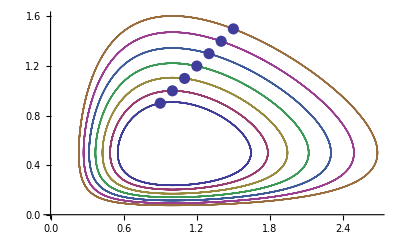

```mathematica
plot1=ParametricPlot[table5,{t,10,50}];
plot2=ListPlot[Table[{i,i},{i,.9,1.5,.1}],PlotStyle->PointSize[.02]];
Show[plot1,plot2]
```

# Question 06

```mathematica
Clear[x,t,u]
```

```mathematica
eq=D[u[x,t],{x,2}]==D[u[x,t],{t,2}]
init={u[x,0]->3*x, Derivative[0,1][u][x,0]->Sin[2*x]}
lp=LaplaceTransform[eq,t,s]/.init
sol=DSolve[lp,u[x,t],x][[1,1,2]]
u[x,s]==sol
ilp=InverseLaplaceTransform[sol,s,t]
Plot3D[ilp,{x,-10,10},{t,0,5},ColorFunction->"Rainbow"]
```

u^(2,0)[x,t]==u^(0,2)[x,t]

{u[x,0]→3 x,u^(0,1)[x,0]→Sin[2 x]}

LaplaceTransform[u^(2,0)[x,t],t,s]==-3 s x+s^2 LaplaceTransform[u[x,t],t,s]-Sin[2 x]

ⅇ^(s x) C[1]+ⅇ^(-s x) C[2]+(12 x+3 s^2 x+s Sin[2 x])/(4+s^2)

u[x,s]==ⅇ^(s x) C[1]+ⅇ^(-s x) C[2]+(12 x+3 s^2 x+s Sin[2 x])/(4+s^2)

C[2] DiracDelta[t-x]+C[1] DiracDelta[t+x]+3 x (DiracDelta[t]-2 Sin[2 t])+6 x Sin[2 t]+Cos[2 t] Sin[2 x]

-Graphics3D-

LaplaceTransform[u^(2,0)[x,t],t,s]==-3 s x+s^2 LaplaceTransform[u[x,t],t,s]-Sin[2 x]

ⅇ^(s x) C[1]+ⅇ^(-s x) C[2]+(12 x+3 s^2 x+s Sin[2 x])/(4+s^2)

u[x,s]==ⅇ^(s x) C[1]+ⅇ^(-s x) C[2]+(12 x+3 s^2 x+s Sin[2 x])/(4+s^2)

C[2] DiracDelta[t-x]+C[1] DiracDelta[t+x]+3 x (DiracDelta[t]-2 Sin[2 t])+6 x Sin[2 t]+Cos[2 t] Sin[2 x]

-Graphics3D-